```mathematica
(*Project 2 : Nikitaras*)

(*Task 1*)

Clear["Global`*"]
```

1. JacobiCN[0.333333 t,0.2]

1.33333 JacobiSN[0.333333 t,0.2]

2. JacobiDN[0.333333 t,0.2]

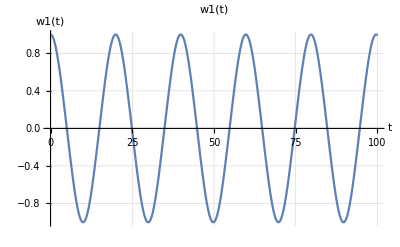

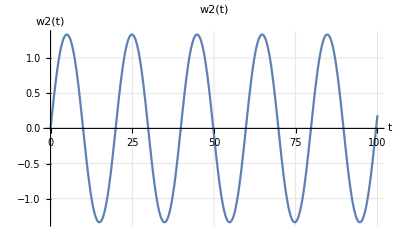

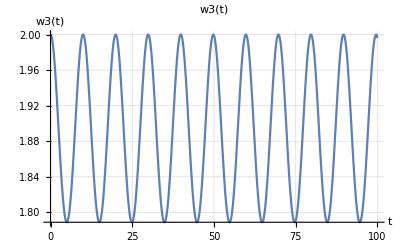

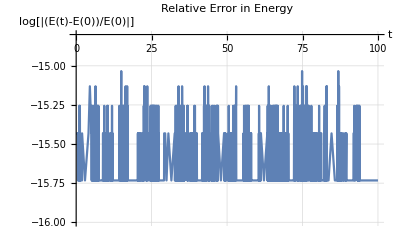

```mathematica
(*Parameter Initialization (I1,I2,I3, w1(0),w2(0),w3(0)*)
I1 = 0.8;
I2 = 0.9;
I3 = 1;
w1o = 1;
w2o = 0;
w3o = 2;
En = (I1*w1o^2 + I2*w2o^2 + I3*w3o^2)/2; (* Calculate Initial Energy for above conditions*)
M = Sqrt[(I1*w1o)^2 + (I2*w2o)^2 + (I3*w3o)^2]; (*Calculate Initial Rotational Kinetic Energy for above conditions*)
t1[t_] = Sqrt[(I3 - I2) (M^2 - 2 En I1)/(I1 I2 I3)]* t; (*Initializes a function τ(t) that will be used later as input for the Jacobi Functions*)
ksquared = (I2 - I1)/(I3 - I2) (2 En I3 - M^2)/(M^2 - 2 En I1); (*Initialize a constant ksquared that will be used below as input for the Jacobi Functions*)
w1[t_] = Sqrt[(2 En I3 - M^2)/(I1 (I3 - I1))]*JacobiCN[t1[t], ksquared] (*Compute Analytical Solutions for w1(t),w2(t),w3(t) and print the results*)
w2[t_] = Sqrt[(2 En I3 - M^2)/(I2 (I3 - I2))]*JacobiSN[t1[t], ksquared]
w3[t_] = Sqrt[(M^2 - 2 En I1)/(I3 (I3 - I1))]*JacobiDN[t1[t], ksquared]

Plot[w1[t], {t, 0, 100}, PlotLabel -> "w1(t)", AxesLabel -> {"t", "w1(t)"}, GridLines -> Automatic] (*Plot w1(t),w2(t),w3(t)*)
Plot[w2[t], {t, 0, 100}, PlotLabel -> "w2(t)", AxesLabel -> {"t", "w2(t)"}, GridLines -> Automatic]
Plot[w3[t], {t, 0, 100}, PlotLabel -> "w3(t)", AxesLabel -> {"t", "w3(t)"}, GridLines -> Automatic]

En1[t_] = 1/2 (I1 w1[t]^2 + I2 w2[t]^2 + I3 w3[t]^2); (*Initialize a function En1(t) that calculates the energy E(t)*)
DEn1[t_] = Log[10, Abs[(En1[t] - En)/En]]; (*Calculate the ΔΕ (relative error in energy). We know that theoretically, E(0) is conserved. However analytically E(t) differs from En*)

Plot[DEn1[t], {t, 0, 100}, AxesLabel -> {"t", "log[|(E(t)-E(0))/E(0)|]"}, PlotLabel -> "Relative Error in Energy", PlotRange -> {{0, 100}, {-16,-14.8}},GridLines -> Automatic](*Plot the relative Error in Energy*)
```

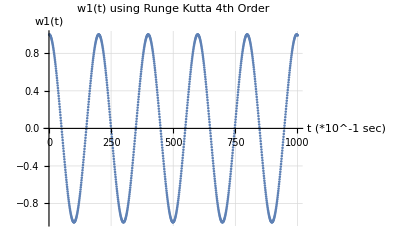

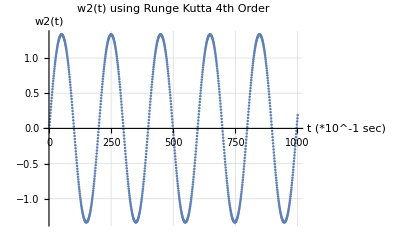

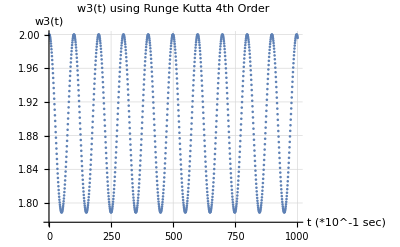

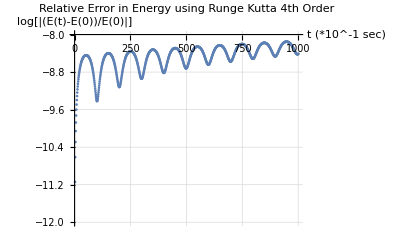

```mathematica
(*Task 2*)

(*Initialize Parameters: Instead of w1(t),w2(t),w3(t), notation of y1(t),y2(t),y3(t) will be used accordingly. i.e. w1(0)=y1(0)=w1o=y1o etc*)
y1o = 1; 
y2o = 0;
y3o = 2;
to = 0; (*Initial time*)
dt = 0.1; (*Time interval dt*)
n = 1001; (*n will be used below for matrix initialization. We need to compute y1 y2 y3 upto tmax=100, with interval dt=0.1. Therefore, we need to compute n=(tmax-to)/dt values of y1 y2 y3, +1 for to=0 to be included.*)
func1[y2_, y3_] = (I2 - I3)*y2*y3/I1; (*First Differential Equation written as function1, in the form y1'(t)=f(y2,y3)*)
func2[y1_, y3_] = (I3 - I1)*y1*y3/I2; (*Second Differential Equation written as function2, in the form y2'(t)=f(y1,y3)*)
func3[y1_, y2_] = (I1 - I2)*y1*y2/I3;(*Third Differential Equation written as function3, in the form y3'(t)=f(y1,y2)*)

(*Initialization of all-zero matrices of size n*)
tar = ConstantArray[0, {n}]; (*tar (t array) will store all values of t*)
y1ar = ConstantArray[0, {n}];(*y1ar (y1 array) will store all values of y1, for every t*)
y2ar = ConstantArray[0, {n}];(*y2ar (y2 array) will store all values of y2, for every t*)
y3ar = ConstantArray[0, {n}];(*y3ar (y3 array) will store all values of y3, for every t*)
ERK4 = ConstantArray[0, {n}];(*ERK4 (Energy Runge Kutta 4th Order) will store all values of energy, for every t*)
Erk4error = ConstantArray[0, {n}];(*Erk4error will store all values of Relative Energy Error, for every t*)

y1ar[[1]] = y1o; (*In each array, the first element is initialized for t=0*)
y2ar[[1]] = y2o;
y3ar[[1]] = y3o;
ERK4[[1]] = En;

For[i = 1, i ≤ n - 1, i++, 
 tar[[i + 1]] = i*dt; (*For Loop that implements the 4th order Runge Kutta Method for a 3x3 system of ODE's.*)
 dy11 = dt*func1[y2ar[[i]], y3ar[[i]]];
 dy21 = dt*func2[y1ar[[i]], y3ar[[i]]];
 dy31 = dt*func3[y1ar[[i]], y2ar[[i]]];
 dy12 = dt*func1[y2ar[[i]] + dy21/2, y3ar[[i]] + dy31/2];
 dy22 = dt*func2[y1ar[[i]] + dy11/2, y3ar[[i]] + dy31/2];
 dy32 = dt*func3[y1ar[[i]] + dy11/2, y2ar[[i]] + dy21/2];
 dy13 = dt*func1[y2ar[[i]] + dy22/2, y3ar[[i]] + dy32/2];
 dy23 = dt*func2[y1ar[[i]] + dy12/2, y3ar[[i]] + dy32/2];
 dy33 = dt*func3[y1ar[[i]] + dy12/2, y2ar[[i]] + dy22/2];
 dy14 = dt*func1[y2ar[[i]] + dy23, y3ar[[i]] + dy33];
 dy24 = dt*func2[y1ar[[i]] + dy13, y3ar[[i]] + dy33];
 dy34 = dt*func3[y1ar[[i]] + dy13, y2ar[[i]] + dy23];
 y1ar[[i + 1]] = y1ar[[i]] + 1/6*(dy11 + 2 dy12 + 2 dy13 + dy14); (*Store computed y1 value in y1ar*)
 y2ar[[i + 1]] = y2ar[[i]] + 1/6*(dy21 + 2 dy22 + 2 dy23 + dy24); (*Store computed y2 value in y2ar*)
 y3ar[[i + 1]] = y3ar[[i]] + 1/6*(dy31 + 2 dy32 + 2 dy33 + dy34);(*Store computed y3 value in y3ar*)
 ERK4[[i + 1]] = (I1*y1ar[[i + 1]]^2 + I2*y2ar[[i + 1]]^2 + I3*y3ar[[i + 1]]^2)/2;(*Store computed Energy value in ERK4*)
 Erk4error[[i + 1]] = Log[10, Abs[(ERK4[[i + 1]] - En)/En]]](*Store computed Relative Energy Error value in Erk4error*)
ListPlot[y1ar, PlotLabel -> "w1(t) using Runge Kutta 4th Order", AxesLabel -> {"t (*10^-1 sec)", "w1(t)"}, GridLines -> Automatic] (*Create a scatter plot of (x,y)=(t,y1)*)

ListPlot[y2ar, PlotLabel -> "w2(t) using Runge Kutta 4th Order",AxesLabel -> {"t (*10^-1 sec)", "w2(t)"}, GridLines -> Automatic](*Create a scatter plot of (x,y)=(t,y2)*)
ListPlot[y3ar, PlotLabel -> "w3(t) using Runge Kutta 4th Order", AxesLabel -> {"t (*10^-1 sec)", "w3(t)"}, GridLines -> Automatic](*Create a scatter plot of (x,y)=(t,y3)*)
ListPlot[Erk4error, AxesLabel -> {"t (*10^-1 sec)", "log[|(E(t)-E(0))/E(0)|]"}, PlotRange -> {{0, 1000}, {-12, -8}}, PlotLabel -> "Relative Error in Energy using Runge Kutta 4th Order", GridLines ->  Automatic](*Create a scatter plot of Relative Energy Error (t,Erk4error)*)
```

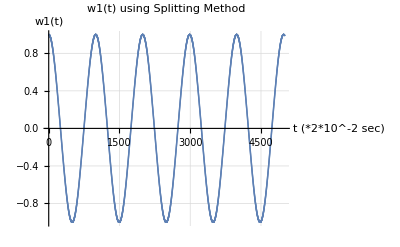

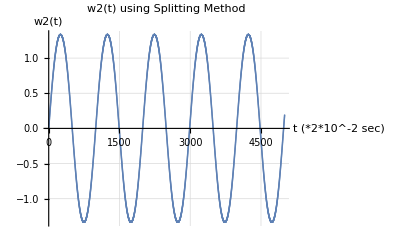

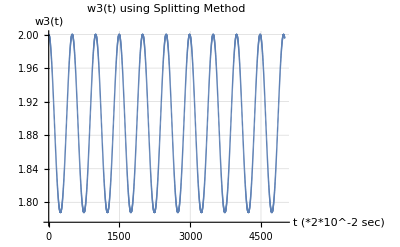

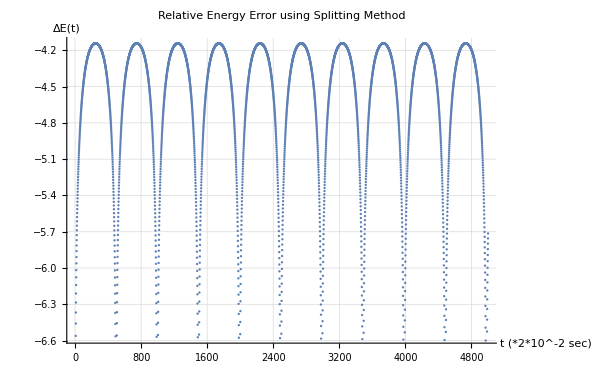

```mathematica
(*We observe that the Relative Error of the Energy using the RK-4th order Method, increases as time passes. For t~0, the Relative error is infinitesimal. However for t>0, the error increases. Furthermore, we observe a periodic pattern of error. Every 10seconds, the error becomes locally minimum.*)

(*Task 3*)
Rx[theta_] = {{1, 0, 0}, {0, Cos[theta], Sin[theta]}, {0, -Sin[theta],Cos[theta]}};
Ry[theta_] = {{Cos[theta], 0, -Sin[theta]}, {0, 1, 0}, {Sin[theta], 0,Cos[theta]}};
Rz[theta_] = {{Cos[theta], Sin[theta], 0}, {-Sin[theta], Cos[theta], 0}, {0, 0, 1}};
M1o = 0.8;
M2o = 0;
M3o = 2;
dt1 = 0.02;
n1 = IntegerPart[1 + 100/dt1];
Mo = Transpose[{M1o, M2o, M3o}];
Resultsw1 = ConstantArray[0, {n1}];
Resultsw2 = ConstantArray[0, {n1}];
Resultsw3 = ConstantArray[0, {n1}];
ESplit = ConstantArray[ 0, {n1}];(*ESplit will store all values of energy, for every t*)
ESplitErr = ConstantArray[0, {n1}];(*ESplitErr will store all values of Relative Energy Error,for every t*)


For[t = 0, t ≤ 5000, t++, Mnew = Rx[M1o*dt1/(2*I1)] . Mo; 
 M1o = Mnew[[1]]; M2o = Mnew[[2]]; M3o = Mnew[[3]]; 
 Mo = Transpose[{M1o, M2o, M3o}];
 Mnew = Ry[M2o*dt1/(2*I2)] . Mo; M1o = Mnew[[1]]; M2o = Mnew[[2]]; 
 M3o = Mnew[[3]]; Mo = Transpose[{M1o, M2o, M3o}];
 Mnew = Rz[M3o*dt1/I3] . Mo; M1o = Mnew[[1]]; M2o = Mnew[[2]]; 
 M3o = Mnew[[3]]; Mo = Transpose[{M1o, M2o, M3o}];
 Mnew = Ry[M2o*dt1/(2*I2)] . Mo; M1o = Mnew[[1]]; M2o = Mnew[[2]]; 
 M3o = Mnew[[3]]; Mo = Transpose[{M1o, M2o, M3o}];
 Mnew = Rx[M1o*dt1/(2*I1)] . Mo; M1o = Mnew[[1]]; M2o = Mnew[[2]]; 
 M3o = Mnew[[3]]; Mo = Transpose[{M1o, M2o, M3o}];
 Resultsw1[[t + 1]] = Mnew[[1]]/I1; Resultsw2[[t + 1]] = Mnew[[2]]/I2; 
 Resultsw3[[t + 1]] = Mnew[[3]]/I3;
ESplit[[t +1]] = (I1*Resultsw1[[t + 1]]^2 + I2*Resultsw2[[t + 1]]^2 + I3*Resultsw3[[t + 1]]^2)/2;(*Store computed Energy value in ERK4*)
ESplitErr[[t + 1]] =  Log[10, Abs[(ESplit[[t + 1]] - En)/ En]]](*Store computed Relative Energy Error value in Erk4error*)
 
ListPlot[Resultsw1, PlotLabel -> "w1(t) using Splitting Method", AxesLabel -> {"t (*2*10^-2 sec)", "w1(t)"}, GridLines -> Automatic] (*Create a scatterplot of (x,y)=(t,w1)*)
ListPlot[Resultsw2, PlotLabel -> "w2(t) using Splitting Method", AxesLabel -> {"t (*2*10^-2 sec)", "w2(t)"}, GridLines -> Automatic] (*Create a scatter plot of (x,y)=(t,w2)*)
ListPlot[Resultsw3, PlotLabel -> "w3(t) using Splitting Method", AxesLabel -> {"t (*2*10^-2 sec)", "w3(t)"}, GridLines -> Automatic] (*Create a scatter plot of (x,y)=(t,w3)*)
 ListPlot[ESplitErr, PlotLabel -> "Relative Energy Error using Splitting Method", AxesLabel -> {"t (*2*10^-2 sec)", "ΔΕ(t)"}, GridLines -> Automatic] (*Create a scatter plot of (x,y)=(t,w1)*)
```

```mathematica
(*We observe that the Relative Error of the Energy using the Splitting Method demonstrates a clear periodic pattern of error. Every 5 seconds (t=0,t=5,t=10s etc) the error becomes infinitesimal.*)
```